## Excision Radius Calculations

Investigating the excision radius function for the case of the BH.
The following parameters were considered: β=1, r_0=8 ,R_0=1.5, R_∞=1.9, Δ=0.05

```mathematica
β=1;r0=8;R0=1.5;Ri=1.9;Δ=0.05;
```

```mathematica
Recc[r_,c_]:=Ri(r/c)^β(1+(r/c)^(1/Δ))^(-β Δ)
Rcirc[r_]:=R0(r/r0)^β
```

Let’s root find a c for Recc that would set Recc=!=Rcirc when r=8M. In otherwords R_0=R_∞(r/c)^β(1+(r/c)^(1/Δ))^(-β Δ).

```mathematica
crule=NSolve[Recc[6,c]==R0,c,Reals][[1]]
Recc[9,c]/.crule
Recc2[r_]:=Recc[r,c]/.crule
```

{c→7.59662}

1.89685

Plotting out the two functions. Expectations: They must intersect at 8M (our “initial condition”).

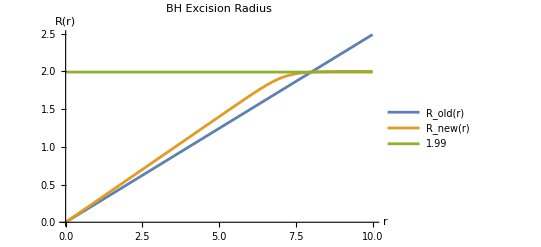

```mathematica
Plot[{Rcirc[r],Recc2[r],Recc[r,8],1.99},{r,0,10},AxesLabel->{"r","R(r)"},PlotLegends->{"R_old(r)","R_new(r)",1.99},PlotLabel->"BH Excision Radius"]
```

## KS ϕ Calculations

The KS coordinates are defined according to https://spectre-code.org/classgr_1_1KerrSchildCoords.html as follows:

```mathematica
x=√(rks^2+a^2)Sin[θ]Cos[φ+ArcTan[a/rks]]
y=√(rks^2+a^2)Sin[θ]Sin[φ+ArcTan[a/rks]]
z=rks Cos[θ]
(JacKStoCart=D[{t,x,y,z},{{t,rks,θ,φ}}]//FullSimplify)//MatrixForm
(JacCarttoKS=Inverse[JacKStoCart]//FullSimplify)//MatrixForm
x^2+y^2+z^2//FullSimplify
ArcTan[y/x]//FullSimplify
```

√(a^2+rks^2) Cos[φ+ArcTan[a/rks]] Sin[θ]

√(a^2+rks^2) Sin[θ] Sin[φ+ArcTan[a/rks]]

rks Cos[θ]

(1 | 0 | 0 | 0
0 | (√(1+a^2/rks^2) rks Cos[φ] Sin[θ])/(√(a^2+rks^2)) | √(a^2+rks^2) Cos[θ] Cos[φ+ArcTan[a/rks]] | -√(a^2+rks^2) Sin[θ] Sin[φ+ArcTan[a/rks]]
0 | (√(1+a^2/rks^2) rks Sin[θ] Sin[φ])/(√(a^2+rks^2)) | √(a^2+rks^2) Cos[θ] Sin[φ+ArcTan[a/rks]] | √(a^2+rks^2) Cos[φ+ArcTan[a/rks]] Sin[θ]
0 | Cos[θ] | -rks Sin[θ] | 0)

(1 | 0 | 0 | 0
0 | (2 rks √(a^2+rks^2) Cos[φ+ArcTan[a/rks]] Sin[θ])/(a^2+2 rks^2+a^2 Cos[2 θ]) | (2 rks √(a^2+rks^2) Sin[θ] Sin[φ+ArcTan[a/rks]])/(a^2+2 rks^2+a^2 Cos[2 θ]) | (2 (a^2+rks^2) Cos[θ])/(a^2+2 rks^2+a^2 Cos[2 θ])
0 | (2 √(a^2+rks^2) Cos[θ] Cos[φ+ArcTan[a/rks]])/(a^2+2 rks^2+a^2 Cos[2 θ]) | (2 √(a^2+rks^2) Cos[θ] Sin[φ+ArcTan[a/rks]])/(a^2+2 rks^2+a^2 Cos[2 θ]) | -(2 rks Sin[θ])/(a^2+2 rks^2+a^2 Cos[2 θ])
0 | -(2 Sin[θ] (√(1+a^2/rks^2) rks^2 Sin[φ]+(a^2+rks^2) Cot[θ]^2 Sin[φ+ArcTan[a/rks]]))/(√(a^2+rks^2) (a^2+2 rks^2+a^2 Cos[2 θ])) | (2 ((a^2+rks^2) Cos[θ] Cos[φ+ArcTan[a/rks]] Cot[θ]+√(1+a^2/rks^2) rks^2 Cos[φ] Sin[θ]))/(√(a^2+rks^2) (a^2+2 rks^2+a^2 Cos[2 θ])) | (2 a Cos[θ])/(a^2+2 rks^2+a^2 Cos[2 θ]))

1/2 (a^2+2 rks^2-a^2 Cos[2 θ])

ArcTan[Tan[φ+ArcTan[a/rks]]]

Now we consider the coordinate transformation for BL coordinate which is the oblate spheroidal transformation

```mathematica
x2=√(rbl^2+a^2)Sin[θ]Cos[ϕ]
y2=√(rbl^2+a^2)Sin[θ]Sin[ϕ]
z2=rbl Cos[θ]
(JacBLtoCart=D[{t,x2,y2,z2},{{t,rbl,θ,ϕ}}]//FullSimplify)//MatrixForm
```

√(a^2+rbl^2) Cos[ϕ] Sin[θ]

√(a^2+rbl^2) Sin[θ] Sin[ϕ]

rbl Cos[θ]

(1 | 0 | 0 | 0
0 | (rbl Cos[ϕ] Sin[θ])/(√(a^2+rbl^2)) | √(a^2+rbl^2) Cos[θ] Cos[ϕ] | -√(a^2+rbl^2) Sin[θ] Sin[ϕ]
0 | (rbl Sin[θ] Sin[ϕ])/(√(a^2+rbl^2)) | √(a^2+rbl^2) Cos[θ] Sin[ϕ] | √(a^2+rbl^2) Cos[ϕ] Sin[θ]
0 | Cos[θ] | -rbl Sin[θ] | 0)

Now we combine everything

```mathematica
(JacBLtoKS=JacCarttoKS.JacBLtoCart/.{rbl->rks,φ->ϕ-ArcTan[a/rks]}//FullSimplify)//MatrixForm
```

(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | a/(a^2+rks^2) | 0 | 1)

Transforming a contravariant-vector in GR goes as: V'^α=(∂x'^α)/(∂x^β)V^β. The 4-velocity is (ṫ,  ṙ, θ̇, ϕ̇ )^T.

```mathematica
(angvelKS=JacBLtoKS.{{tdot},{rdot},{θdot},{ϕdot}})//MatrixForm
angvelKS[[4]]/angvelKS[[1]]/.rdot->0/.rks->8
```

(tdot
rdot
θdot
(a rdot)/(a^2+rks^2)+ϕdot)

{ϕdot/tdot}

From this we recognise for the formula: dϕ/dt=dφ/dt in the circular limit. Directly reading off the coordinates between BL and KS obtains us the same Jacobian

```mathematica
Inverse[D[{t,rks,θ,φ+ArcTan[a/rks]},{{t,rks,θ,φ}}]]//FullSimplify//MatrixForm
```

(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | a/(a^2+rks^2) | 0 | 1)

Now let’s compute the angular velocity and the velocity of circular orbits. From Bardeen (1972) et. al., the angular velocity for a circular orbit is dϕ/dt=1/(r^(3/2)+a).